```mathematica
homdirectory=ParentDirectory[NotebookDirectory[]]; (*set home directory here*)
SetDirectory[homdirectory];
figpath="\figures";
```

## Functions and parameters

```mathematica
greekletter[l_]:=Style[l/.{Alpha->α, Beta->β, Gamma->γ, Rho->ρ, Lambda ->λ},FontFamily->"Stencil", FontSize->16]
```

```mathematica
alpha=4;
l=8;
multiplicity=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
w[k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[k,d],{d,0,l},{k,0,l}];
MapPartialVal[list_,data_,height_]:=Module[{Ab},
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];
Ab.data
]
ck = Table[Table[2^k (-1)^q Binomial[k,q],{q,0,l}],{k,0,l}];
mk=Table[Table[PadLeft[ck[[k]],l+d][[;;l+1]],{d,1,l+1}],{k,l+1}];
```

```mathematica
Nbyfirst[x_]:=First[x]^-1 x
Nbysum[x_]:=Total[x]^-1 x
```

```mathematica
a0=12;
a1=1.5;
a2=0.8;
```

```mathematica
fontsize=22;
fstyle=Table[{GrayLevel[.3],AbsoluteThickness[1]},4];
```

```mathematica
imagesize=400;
```

```mathematica
loglambsfit=Table[a0/(1 + Exp[ a1 (x - a2)]) ,{x,l}];
lambdascorrected=Nbyfirst@(Exp[loglambsfit] - .99);
lambdasproper=PadLeft[lambdascorrected,l+1];
vc=Transpose@{Range[1,l],Nbysum[Rest[lambdasproper]*Rest@multiplicity]};
ps=Table[{Black,Opacity[vc[[i,2]]]},{i,Length[vc]}];texts={"1st order (w=","2nd order (w=", "3rd order (w=","4th order (w=","5th order (w=", "6th order (w=", "7th order (w=", "8th order (w="};labs=Style[#,FontSize->12, FontFamily->"Helvetica"]&/@Table[StringJoin[texts[[i]],")", ToString[Round[vc[[i,2]],.01]]],{i,Length[texts]}];
```

```mathematica
startdist=0;
```

```mathematica
rho=Nbyfirst@(wkd[[All,2;;]].Rest[lambdasproper]);
plotdat=Transpose@{Range[0,l],Nbyfirst[rho]};
figrho=Show[
ListLinePlot[
plotdat[[startdist+1;;]],
Frame->True,
Axes->True,
AxesStyle->Directive[Gray,Dashed],
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",greekletter[Rho]},FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotStyle->GrayLevel[.5],
PlotRange->{{startdist,l+.1},{-.3,1}},
BaseStyle->{FontSize->fontsize},
ImageSize->imagesize,
AspectRatio->.75,
PlotRangeClipping->False],
ListPlot[
plotdat[[startdist+1;;]],
PlotStyle->{Black,PointSize[.02]}
]
];
```

```mathematica
figVCBar=BarChart[vc[[All,2]],ChartLabels->vc[[All,1]],
Frame->True,
FrameLabel->{"Interaction order","Variance explained"},
FrameTicks->{{Range[0,1,.1]/.{0.->0},None},{Range[1,l,1],None}},
FrameStyle->fstyle,
BaseStyle->{FontSize->fontsize},
ChartStyle->GrayLevel[.25],
ImageSize->imagesize,
PlotRange->{{.5,l+.5},{0,0.59}},
PlotRangePadding->False,
PlotRangeClipping->False,
AspectRatio->.75
];
```

```mathematica
plotdat=Transpose@{Range[1,l],Rest[lambdasproper]};
figlambda=Show[
ListLogPlot[
plotdat,
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Interaction order",greekletter[Lambda]},
Joined->True,
PlotRange->{{1,l+.1},{10^-4.5, 1}},
PlotRangeClipping->None,
FrameTicks->{{{{1,1},{10^-1, Superscript[10,-1]},{10^-2, Superscript[10,-2]},{10^-3, Superscript[10,-3]},{10^-4, Superscript[10,-3]}},None},{Range[0,l,1]/.{0.->0},None}},
PlotStyle->GrayLevel[.5],
BaseStyle->{FontSize->fontsize},
ImageSize->imagesize,
AspectRatio->.75],
ListLogPlot[
plotdat,
PlotStyle->{Black,PointSize[.02]}
]
];
```

```mathematica
w[l_,k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
```

```mathematica
gammak=Nbyfirst/@Table[Table[w[l-k0,k,d],{d,0,l-k0},{k,0,l-k0}].lambdasproper[[k0 +1;;]],{k0,1,l}];
figgamma=Table[Module[{plotdat},
plotdat=Transpose@{Range[0,Length[gammak[[k]]]-1],Nbyfirst[gammak[[k]]]};
Show[
ListLinePlot[
plotdat[[startdist+1;;]],
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],ToString[k]]},FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
PlotStyle->GrayLevel[.5],
PlotRange->{{startdist,l+.1},{-.12,1}},
PlotRangeClipping->False,
BaseStyle->{FontSize->fontsize},
ImageSize->imagesize,
AspectRatio->.75],
ListPlot[
plotdat[[startdist+1;;]],
PlotStyle->{Black,PointSize[.02]}]]
],{k,1,3}];
```

Have the dashed line be prolog.

```mathematica
labelfigs[figs_]:=Table[
Labeled[figs[[i]],Style[FromCharacterCode[64+i],Bold,FontFamily->"Helvetica",FontSize->fontsize],{{Top,Left}}],
{i,Length[figs]}
]
```

## Figure 1

### Wk

```mathematica
colorlist1=Partition[{240,249,232,
186,228,188,
123,204,196,
67,162,202,
8,104,172},3]/255;
```

```mathematica
colorlist1=Partition[{215,25,28,
253,174,97,
255,255,191,
171,217,233,
44,123,182},3]/255;
```

```mathematica
colorlist1=Partition[{208,209,230,
166,189,219,
116,169,207,
43,140,190,
4,90,141},3]/255;
```

```mathematica
colors1=RGBColor/@colorlist1//Reverse
```

{RGBColor[{Rational[4, 255], Rational[6, 17], Rational[47, 85]}],RGBColor[{Rational[43, 255], Rational[28, 51], Rational[38, 51]}],RGBColor[{Rational[116, 255], Rational[169, 255], Rational[69, 85]}],RGBColor[{Rational[166, 255], Rational[63, 85], Rational[73, 85]}],RGBColor[{Rational[208, 255], Rational[209, 255], Rational[46, 51]}]}

```mathematica
wklabs1=Style[#,FontFamily->"Helvetica",FontSize->14]&/@{"1st order", "2nd order", "3rd order", "4th order", "5th order"};
wklabs2=Style[#,FontFamily->"Helvetica",FontSize->14]&/@{"6th order", "7th order", "8th order"};
```

```mathematica
figWcor=ListLinePlot[Nbyfirst/@Transpose[wkd][[2;;6]],
DataRange->{0,l},
BaseStyle->{FontSize->fontsize},
PlotStyle->colors1,
PlotRange->{{0,l+.1},{-.4,1}},
ImageSize->400,
AspectRatio->.75,
Frame->True,
FrameStyle->fstyle,
AxesStyle->Directive[Gray,Dashed],
Method->{"AxesInFront"->False},
FrameLabel->{"Hamming Distance",greekletter[Rho]},
FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotLegends->Placed[LineLegend[Automatic,wklabs1,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.8,.6}],
PlotRangeClipping->False
];
```

```mathematica
colorlist2=Partition[{224,236,244,
158,188,218,
136,86,167},3]/255;
```

```mathematica
colorlist2=Partition[{237,248,251,
178,226,226,
102,194,164,
35,139,69},3]/255;
```

```mathematica
colors2=RGBColor/@colorlist2//Reverse
```

{RGBColor[{Rational[7, 51], Rational[139, 255], Rational[23, 85]}],RGBColor[{Rational[2, 5], Rational[194, 255], Rational[164, 255]}],RGBColor[{Rational[178, 255], Rational[226, 255], Rational[226, 255]}],RGBColor[{Rational[79, 85], Rational[248, 255], Rational[251, 255]}]}

```mathematica
figWanticor=ListLinePlot[Nbyfirst/@Transpose[wkd][[7;;]],
DataRange->{0,l},
BaseStyle->{FontSize->fontsize},
PlotStyle->colors2,
PlotRange->{{0,l+.1},{-.4,1}},
ImageSize->400,
AspectRatio->.75,
Frame->True,
FrameStyle->fstyle,
AxesStyle->Directive[Gray,Dashed],
FrameLabel->{"Hamming Distance",greekletter[Rho]},
FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotLegends->Placed[LineLegend[Automatic,wklabs2,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.8,.6}],
PlotRangeClipping->False
];
```

### rho

```mathematica
ps=Table[{Black,Opacity[vc[[i,2]]]},{i,Length[vc]}];
texts={"1st order","2nd order", "3rd order","4th order","5th order", "6th order", "7th order", "8th order"};
labs=Style[#,FontSize->12, FontFamily->"Helvetica"]&/@Table[texts[[k]]<>" ("<>ToString[Subscript["v",ToString[k]],StandardForm]<>"="<>ToString[Round[vc[[k,2]],.01]]<>")",{k,l}]
```

{1st order (v_1=0.52),2nd order (v_2=0.15),3rd order (v_3=0.11),4th order (v_4=0.08),5th order (v_5=0.06),6th order (v_6=0.04),7th order (v_7=0.03),8th order (v_8=0.01)}

```mathematica
plotdat=Transpose@{Range[0,l],Nbyfirst[rho]};
figrho2=Show[
ListLinePlot[Nbyfirst/@Transpose[wkd][[2;;]],
DataRange->{0,l},
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",greekletter[Rho]},
AxesStyle->Directive[Gray,Dashed],
BaseStyle->{FontSize->fontsize},
PlotStyle->ps,
ImageSize->400,
AspectRatio->.75,
PlotRange->{{0,l+.1},{-.4,1}},
PlotRangeClipping->False,
FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotLegends->Placed[LineLegend[Automatic,labs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.1,LegendMargins->0,Alignment->Right],{.78,.7}]
],
ListLinePlot[
plotdat,
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",greekletter[Rho]},FrameTicks->{{Range[0,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotStyle->GrayLevel[0],
BaseStyle->{FontSize->fontsize},
AspectRatio->.75],
ListPlot[
plotdat,
PlotStyle->{Black,PointSize[.02]}
]
];
```

### 7 panel figure

```mathematica
labelfigs[figs_]:=Table[
Show[figs[[i]], Epilog->Text[Style[FromCharacterCode[64+i],Bold,FontFamily->"Helvetica", FontSize->fontsize],ImageScaled@{0.05,.95}],ImagePadding->{{80,5},{60,10}}],
{i,Length[figs]}
]
```

```mathematica
panels=labelfigs@{figVCBar, figgamma[[1]], figgamma[[2]],figgamma[[3]],figWcor, figWanticor, figrho2};
```

```mathematica
fig1=Column[{Grid[{panels[[;;4]]}],Grid[{panels[[5;;]]}]},Alignment->Center, Spacings->{1,2}];
```

```mathematica
Export[StringJoin[figpath, "/Fig1.pdf"],fig1];
```

## Supplemental figure 1

```mathematica
homdirectory="/Users/keitokiddo/VC";
SetDirectory[homdirectory];
```

```mathematica
alpha=4;
l=8;
multiplicity=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
w[l_,k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[k,d],{d,0,l},{k,0,l}];
MapPartialVal[list_,data_,height_]:=Module[{Ab},
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];
Ab.data
]
ck = Table[Table[2^k (-1)^q Binomial[k,q],{q,0,l}],{k,0,l}];
mk=Table[Table[PadLeft[ck[[k]],l+d][[;;l+1]],{d,1,l+1}],{k,l+1}];
```

```mathematica
greekletter[l_]:=Style[l/.{Alpha->α, Beta->β, Gamma->γ, Rho->ρ, Lambda ->λ},FontFamily->"Stencil", FontSize->16]
Nbyfirst[x_]:=First[x]^-1 x
Nbysum[x_]:=Total[x]^-1 x
labelfigs[figs_]:=Table[
Labeled[figs[[i]],Style[FromCharacterCode[64+i],Bold,FontFamily->"Helvetica",FontSize->fontsize],{{Top,Left}}],
{i,Length[figs]}
]
```

```mathematica
fontsize=18;
fstyle=Table[{GrayLevel[.3],Thickness[.006]},4];
```

```mathematica
(*Choose lambdas*)
a0=12;
a1=1.5;
a2=0.8;
loglambsfit=Table[a0/(1 + Exp[ a1 (x - a2)]) ,{x,l}];
lambdascorrected=Nbyfirst@(Exp[loglambsfit] - .99);
lambdasproper=PadLeft[lambdascorrected,l+1];
```

#### Wk

```mathematica
colorlist1=Partition[{240,249,232,
186,228,188,
123,204,196,
67,162,202,
8,104,172},3]/255;
```

```mathematica
colorlist1=Partition[{215,25,28,
253,174,97,
255,255,191,
171,217,233,
44,123,182},3]/255;
```

```mathematica
colorlist1=Partition[{208,209,230,
166,189,219,
116,169,207,
43,140,190,
4,90,141},3]/255;
```

```mathematica
colors1=RGBColor/@colorlist1//Reverse
```

{RGBColor[{Rational[4, 255], Rational[6, 17], Rational[47, 85]}],RGBColor[{Rational[43, 255], Rational[28, 51], Rational[38, 51]}],RGBColor[{Rational[116, 255], Rational[169, 255], Rational[69, 85]}],RGBColor[{Rational[166, 255], Rational[63, 85], Rational[73, 85]}],RGBColor[{Rational[208, 255], Rational[209, 255], Rational[46, 51]}]}

```mathematica
wklabs1=Style[#,FontFamily->"Helvetica",FontSize->14]&/@{"1st order", "2nd order", "3rd order", "4th order", "5th order"};
wklabs2=Style[#,FontFamily->"Helvetica",FontSize->14]&/@{"6th order", "7th order", "8th order"};
```

```mathematica
wkdamp=Transpose@Join[ConstantArray[0,{2,7}],Transpose@Table[w[6, k,d],{d,0,l-2},{k,0,l-2}]];
```

```mathematica
Do[wkdamp[[All,k]]=wkdamp[[All,k]]/wkdamp[[1,k]],{k,3,l+1}]
```

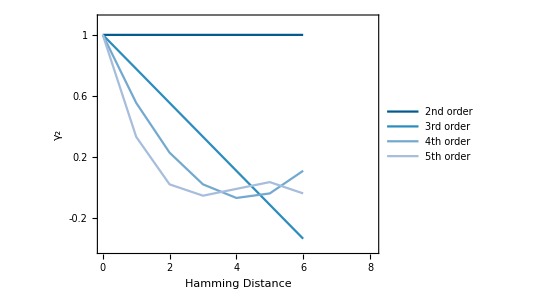

```mathematica
figWcor=Show[ListLinePlot[Transpose[wkdamp][[3;;6]],
DataRange->{0,l-2},
BaseStyle->{FontSize->fontsize},
PlotStyle->colors1,
PlotRange->{{0,8+.1},{-.4,1.1}},
ImageSize->400,
AspectRatio->.75,
Frame->True,
FrameStyle->fstyle,
AxesStyle->Directive[Gray,Dashed],
Method->{"AxesInFront"->False},
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],2]},
FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotLegends->Placed[LineLegend[Automatic,wklabs1[[2;;]],LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.8,.6}]
]]
```

```mathematica
colorlist2=Partition[{224,236,244,
158,188,218,
136,86,167},3]/255;
```

```mathematica
colorlist2=Partition[{237,248,251,
178,226,226,
102,194,164,
35,139,69},3]/255;
```

```mathematica
colors2=RGBColor/@colorlist2//Reverse
```

{RGBColor[{Rational[7, 51], Rational[139, 255], Rational[23, 85]}],RGBColor[{Rational[2, 5], Rational[194, 255], Rational[164, 255]}],RGBColor[{Rational[178, 255], Rational[226, 255], Rational[226, 255]}],RGBColor[{Rational[79, 85], Rational[248, 255], Rational[251, 255]}]}

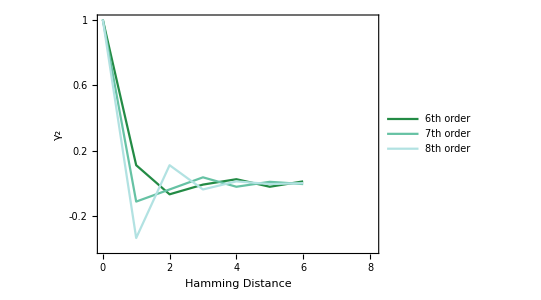

```mathematica
figWanticor=ListLinePlot[Transpose[wkdamp][[7;;]],
DataRange->{0,l-2},
BaseStyle->{FontSize->fontsize},
PlotStyle->colors2,
PlotRange->{{0,8+.1},{-.4,1}},
ImageSize->400,
AspectRatio->.75,
Frame->True,
FrameStyle->fstyle,
AxesStyle->Directive[Gray,Dashed],
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],2]},
FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotLegends->Placed[LineLegend[Automatic,wklabs2,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.8,.6}]
]
```

### rho

Panel C: 
rho: dots = black, connectors: gray, wk: some other color shaded wrt the weights

```mathematica
purple=RGBColor[{117,112,179}/255]
```

RGBColor[{Rational[39, 85], Rational[112, 255], Rational[179, 255]}]

```mathematica
k0=2;
```

```mathematica
G2=Table[w[l-k0,k,d],{d,0,l-k0},{k,0,l-k0}].lambdasproper[[k0 +1;;]];
```

```mathematica
vc2=Nbysum[lambdasproper[[3;;]]*Table[Binomial[l-k0,k](alpha-1)^k, {k,0,l-k0}]]
```

{0.0506906,0.11008,0.171852,0.196277,0.204475,0.182423,0.0842026}

```mathematica
vc2t=NumberForm[Round[#,.01],{2,2}]&/@Nbysum[lambdasproper[[3;;]]*Table[Binomial[l-k0,k](alpha-1)^k, {k,0,l-k0}]]
```

{0.05,0.11,0.17,0.20,0.20,0.18,0.08}

```mathematica
texts={"1st order (w=","2nd order (w=", "3rd order (w=","4th order (w=","5th order (w=", "6th order (w=", "7th order (w=", "8th order (w="};
labs=Style[#,FontSize->12, FontFamily->"Helvetica"]&/@Table[StringJoin[texts[[i+1]], ToString[vc2t[[i]]],")"],{i,7}];
ps=Table[{Black,Opacity[vc2[[i]]]},{i,Length[vc2]}];
```

```mathematica
ps=Table[{Black,Opacity[vc2[[i]]]},{i,Length[vc2]}];
```

```mathematica
texts={"1st order","2nd order", "3rd order","4th order","5th order", "6th order", "7th order", "8th order"};
labs=Style[#,FontSize->12, FontFamily->"Helvetica"]&/@Table[texts[[k+1]]<>" ("<>ToString[Subscript["v",ToString[k]],StandardForm]<>"="<>ToString[vc2t[[k]]]<>")",{k,7}];
```

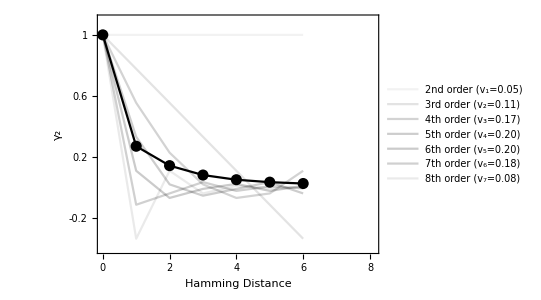

```mathematica
plotdat=Transpose@{Range[0,l-k0],Nbyfirst[G2]};
figrho2=Show[
ListLinePlot[Transpose[wkdamp][[k0+1;;]],
DataRange->{0,l-2},
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],2]},
AxesStyle->Directive[Gray,Dashed],
BaseStyle->{FontSize->fontsize},
PlotStyle->ps,
ImageSize->400,
AspectRatio->.75,
PlotRange->{{0,l+.1},{-.4,1.1}},
PlotRangeClipping->False,
FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotLegends->Placed[LineLegend[Automatic,labs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.1,LegendMargins->0,Alignment->Right],{.78,.6}]
],
ListLinePlot[
plotdat,
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],2]},FrameTicks->{{Range[0,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotStyle->GrayLevel[0],
BaseStyle->{FontSize->fontsize},
AspectRatio->.75,
PlotRange->All],
ListPlot[
plotdat,
PlotStyle->{Black,PointSize[.02]}
]
]
```

```mathematica
Gamma2s=Grid[{labelfigs[{figWcor,figWanticor,figrho2}]},Spacings->{3, 1}]
```

-Graphics-A | -Graphics-B | -Graphics-C

```mathematica
Export["figures/Gamma_2_by_k.pdf",Gamma2s];
```

## Supplemental figure 2

### MEI

```mathematica
m=1;
lambdasME=PadLeft[1/Table[(alpha k)^2 - alpha^2 k,{k,2,l}],l+1];
(*addtive component chosen to account for 80% total variance*)lambdasME[[2]]=29;
```

```mathematica
ListPlot[wkd[[All,2;;]].Rest@lambdasME,PlotRange->All];
vc=Transpose@{Range[1,l],Nbysum[Rest[lambdasME]*Rest@multiplicity]}//N;
vc[[All,2]][[;;1]]//Total
```

0.802246

### additive

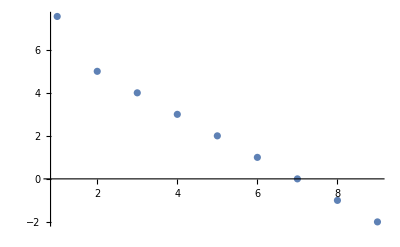

0.800306

```mathematica
m=1;
Kentries=Table[∑_(k=1)^m Binomial[l-d,k],{d,0,l}];
(*noise variance chosen so first three orders account for 80% total variance*)
lambdas1=LinearSolve[wkd,Kentries] + 1.55;
ListPlot[wkd[[All,2;;]].Rest@lambdas1,PlotRange->All]
vc=Transpose@{Range[1,l],Nbysum[Rest[lambdas1]*Rest@multiplicity]}//N;
vc[[All,2]][[;;3]]//Total
```

### pairwise

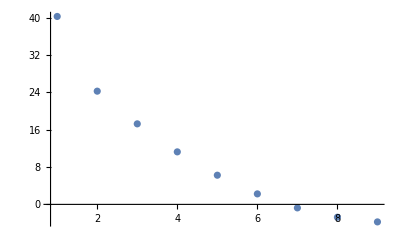

0.802082

```mathematica
m=2;
Kentries=Table[∑_(k=1)^m Binomial[l-d,k],{d,0,l}];
(*noise variance chosen so first three orders account for 80% total variance*)
lambdas2=LinearSolve[wkd,Kentries] + 8;
ListPlot[wkd[[All,2;;]].Rest@lambdas2,PlotRange->All]
vc=Transpose@{Range[1,l],Nbysum[Rest[lambdas2]*Rest@multiplicity]}//N;
vc[[All,2]][[;;m]]//Total
```

### three way

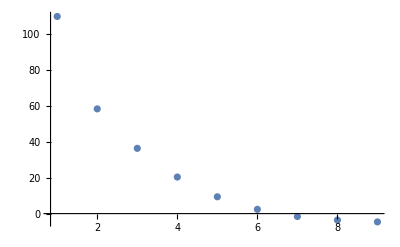

0.800811

```mathematica
m=3;
Kentries=Table[∑_(k=1)^m Binomial[l-d,k],{d,0,l}];
(*noise variance chosen so first three orders account for 80% total variance*)
lambdas3=LinearSolve[wkd,Kentries] + 22.5;
ListPlot[wkd[[All,2;;]].Rest@lambdas3,PlotRange->All]
vc=Transpose@{Range[1,l],Nbysum[Rest[lambdas3]*Rest@multiplicity]}//N;
%[[All,2]][[;;3]]//Total
```

### Plot all panels

```mathematica
makefigure[lambdas_]:=Module[{lambdasproper, vc,rho,figrho,figVCBar,figlambda,gammak,figgamma},
lambdasproper=lambdas;
lambdasproper=lambdasproper/lambdasproper[[2]];
vc=Transpose@{Range[1,l],Nbysum[Rest[lambdasproper]*Rest@multiplicity]}//N;rho=Nbyfirst@(wkd[[All,2;;]].Rest[lambdasproper]);
plotdat=Transpose@{Range[0,l],Nbyfirst[rho]};
figrho=Show[
ListLinePlot[
plotdat[[startdist+1;;]],
Frame->True,
Axes->True,
AxesStyle->Directive[Gray,Dashed],
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",greekletter[Rho]},FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotStyle->GrayLevel[.5],
PlotRange->{{startdist,l+.1},{-.3,1}},
BaseStyle->{FontSize->fontsize},
ImageSize->300,
AspectRatio->.6,
PlotRangeClipping->False],
ListPlot[
plotdat[[startdist+1;;]],
PlotStyle->{Black,PointSize[.02]}
]
];
figVCBar=BarChart[vc[[All,2]],ChartLabels->vc[[All,1]],
Frame->True,
FrameLabel->{"Interaction order","Variance explained"},
FrameTicks->{{Range[0,1,.2]/.{0.->0},None},{Range[1,l,1],None}},
FrameStyle->fstyle,
BaseStyle->{FontSize->fontsize},
ChartStyle->GrayLevel[.25],
ImageSize->300,
PlotRange->{{.5,l+.5},{0,.8}},
PlotRangePadding->False,
PlotRangeClipping->False,
AspectRatio->.6
];

plotdat=Transpose@{Range[1,l],Rest[lambdasproper]};

figlambda=Show[
ListLogPlot[
plotdat,
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Order",greekletter[Lambda]},
Joined->True,
PlotRange->{{1,l+.1},All},
PlotRangeClipping->None,
FrameTicks->{{{{1,1},{10^-1, Superscript[10,-1]},{10^-2, Superscript[10,-2]},{10^-3, Superscript[10,-3]},{10^-4, Superscript[10,-3]}},None},{Range[0,l,1]/.{0.->0},None}},
PlotStyle->GrayLevel[.5],
BaseStyle->{FontSize->fontsize},
ImageSize->300,
AspectRatio->.6],
ListLogPlot[
plotdat,
PlotStyle->{Black,PointSize[.02]}
]
];

gammak=Nbyfirst/@Table[Table[w[l-k0,k,d],{d,0,l-k0},{k,0,l-k0}].lambdasproper[[k0 +1;;]],{k0,1,l}];

figgamma=Table[Module[{plotdat},
plotdat=Transpose@{Range[0,Length[gammak[[k]]]-1],Nbyfirst[gammak[[k]]]};
Show[
ListLinePlot[
plotdat[[startdist+1;;]],
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],ToString[k]]},FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
PlotStyle->GrayLevel[.5],
PlotRange->{{startdist,l+.1},{-.12,1}},
BaseStyle->{FontSize->fontsize},
ImageSize->300,
AspectRatio->.6],
ListPlot[
plotdat[[startdist+1;;]],
PlotStyle->{Black,PointSize[.02]}]]
],{k,1,3}];
fig=Magnify[Grid[ArrayReshape[{figrho,figVCBar,figlambda,figgamma[[1]],figgamma[[2]],figgamma[[3]]},{2,3}],Spacings->{2, .2}],1]

]
```

```mathematica
labs=Style[#,FontFamily->"Helvetica",FontSize->25]&/@{"Additive","Pairwise","Three-way","Minimum epistasis interpolation"};
lambdaslist={lambdas1,lambdas2,lambdas3,lambdasME};
summaryfigbymodel=Grid[Table[{Labeled[makefigure[lambdaslist[[i]]],labs[[i]],{Top}]},{i,4}],Spacings->{0, 3}];
Export["figures/Fig_stats_by_model.pdf",summaryfigbymodel];
```